```mathematica
Table[Sin[(π θ)/4],{θ,0,100}]
```

{0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0}

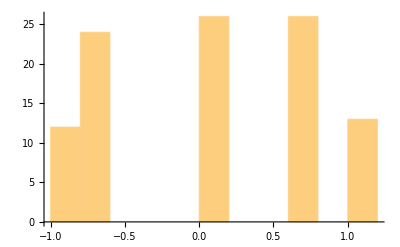

```mathematica
Histogram[Out[1]]
```

```mathematica
Entropy[Out[1]]
```

1/101 (-12 Log[12]-13 Log[13]-24 Log[24]-52 Log[26])+Log[101]

```mathematica
N[1/101 (-12 Log[12]-13 Log[13]-24 Log[24]-52 Log[26])+Log[101]]
```

1.55713

```mathematica
Kurtosis[Out[1]]
```

(101 ((26 (-1-√2)^4)/104060401+12 (-1+1/101 (-1-√2))^4+13 (1+1/101 (-1-√2))^4+24 (-1/(√2)+1/101 (-1-√2))^4+26 (1/(√2)+1/101 (-1-√2))^4))/((26 (-1-√2)^2)/10201+12 (-1+1/101 (-1-√2))^2+13 (1+1/101 (-1-√2))^2+24 (-1/(√2)+1/101 (-1-√2))^2+26 (1/(√2)+1/101 (-1-√2))^2)^2

```mathematica
N[%5]
```

1.51883

```mathematica
With[{L=Function[x,-f[x]Log[f[x]]]},
FullSimplify[
D[L[x],f[x]]-D[D[f[x],f'[x]],x]==0,
Element[x|f[x]|f'[x],Reals]
]]
```

1+Log[f[x]]==0

```mathematica
Reduce[1+Log[f[x]]==0]
```

Log[f[x]]==-1

```mathematica
Solve[Log[f[x]]==-1,{x}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→f^(-1)[1/ⅇ]}}

```mathematica
(f^(-1))[1/ⅇ][x]
```

f^(-1)[1/ⅇ][x]

```mathematica
(f^(-1))[1/ⅇ][1]
```

f^(-1)[1/ⅇ][1]

```mathematica
With[{L=Function[x,√(1+f'[x]^2)]},
FullSimplify[
D[L[x],f[x]]-D[D[f[x],f'[x]],x]==0,
Element[x|f[x]|f'[x],Reals]
]]
```

True

```mathematica
With[{L=Function[x,√(1+f'[x]^2)]},
FullSimplify[
D[L[x],f[x]]-D[D[f[x],f'[x]],x],
Element[x|f[x]|f'[x],Reals]
]]
```

0

```mathematica
With[{L=Function[x,-f[x]Log[f[x]]]},
FullSimplify[
D[L[x],f[x]]-D[D[L[x],f'[x]],x]==0,
Element[x|f[x]|f'[x],Reals]
]]
```

1+Log[f[x]]==0

```mathematica
With[{L=Function[x,√(1+f'[x]^2)]},
FullSimplify[
D[L[x],f[x]]-D[D[L[x],f'[x]],x]==0,
Element[x|f[x]|f'[x],Reals]
]]
```

f''[x]==0

```mathematica
DSolve[f''[x]==0,{f[x]},{x}]
```

{{f[x]→C[1]+x C[2]}}

```mathematica
With[{L=Function[x,f[x] √(1+f'[x]^2)]},
FullSimplify[
D[L[x],f[x]]-D[D[L[x],f'[x]],x]==0,
Element[x|f[x]|f'[x],Reals]
]]
```

1+f'[x]^2==f[x] f''[x]

```mathematica
DSolve[1+f'[x]^2==f[x] f''[x],{f[x],f[x]},{x}]
```

{{f[x]→-(ⅇ^(-C[1]) Tanh[ⅇ^C[1] (x+C[2])])/(√(-1+Tanh[ⅇ^C[1] (x+C[2])]^2))},{f[x]→(ⅇ^(-C[1]) Tanh[ⅇ^C[1] (x+C[2])])/(√(-1+Tanh[ⅇ^C[1] (x+C[2])]^2))}}

```mathematica
(ⅇ^-1 Tanh[ⅇ(x)])/(√(-1+Tanh[ⅇ (x)]^2))
```

Tanh[ⅇ x]/(ⅇ √(-1+Tanh[ⅇ x]^2))

```mathematica
Simplify[Tanh[ⅇ x]/(ⅇ √(-1+Tanh[ⅇ x]^2))]
```

Tanh[ⅇ x]/(ⅇ √(-Sech[ⅇ x]^2))

```mathematica
Plot[Tanh[ⅇ x]/(ⅇ √(-Sech[ⅇ x]^2)),{x,-2,2}]
```

-Graphics-

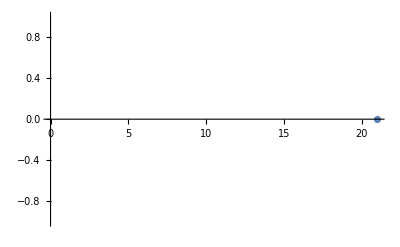

```mathematica
ListPlot[Table[Tanh[ⅇ x]/(ⅇ √(-Sech[ⅇ x]^2)),{x,-2,2,.1}]]
```

```mathematica
Tanh[ⅇ x]/(ⅇ √(-Sech[ⅇ x]^2))
```

Tanh[ⅇ x]/(ⅇ √(-Sech[ⅇ x]^2))

```mathematica
D[Tanh[ⅇ x]/(ⅇ √(-Sech[ⅇ x]^2)), x]
```

Sech[ⅇ x]^2/(√(-Sech[ⅇ x]^2))-(Sech[ⅇ x]^2 Tanh[ⅇ x]^2)/((-Sech[ⅇ x]^2)^(3/2))

```mathematica
DSolve[1+f'[x]^2==f[x] f''[x],{f[x]},{x}]
```

{{f[x]→-(ⅇ^(-C[1]) Tanh[ⅇ^C[1] (x+C[2])])/(√(-1+Tanh[ⅇ^C[1] (x+C[2])]^2))},{f[x]→(ⅇ^(-C[1]) Tanh[ⅇ^C[1] (x+C[2])])/(√(-1+Tanh[ⅇ^C[1] (x+C[2])]^2))}}

```mathematica
(ⅇ^(-C[1]) Tanh[ⅇ^C[1] (x+C[2])])/(√(-1+Tanh[ⅇ^C[1] (x+C[2])]^2))/.{C[1]->1,C[2]->0}
```

Tanh[ⅇ x]/(ⅇ √(-1+Tanh[ⅇ x]^2))

```mathematica
Plot[Tanh[ⅇ x]/(ⅇ √(-1+Tanh[ⅇ x]^2)),{x,-20,20}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

```mathematica
Tanh[ⅇ x]
```

Tanh[ⅇ x]

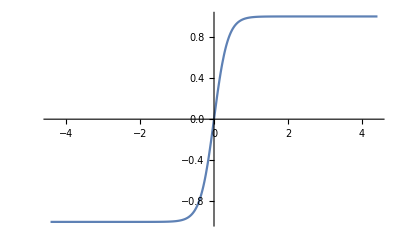

```mathematica
Plot[Tanh[ⅇ x],{x,-4.414553294057308,4.414553294057308}]
```

```mathematica
ⅇ √(-1+Tanh[ⅇ x]^2)
```

ⅇ √(-1+Tanh[ⅇ x]^2)

```mathematica
Plot[ⅇ √(-1+Tanh[ⅇ x]^2),{x,-2,2}]
```

-Graphics-

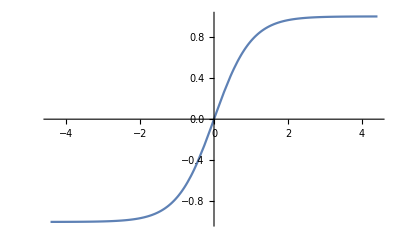

```mathematica
Plot[Tanh[x],{x,-4.414553294057308,4.414553294057308}]
```

```mathematica
CDF[NormalDistribution[],x]
```

1/2 Erfc[-x/(√2)]

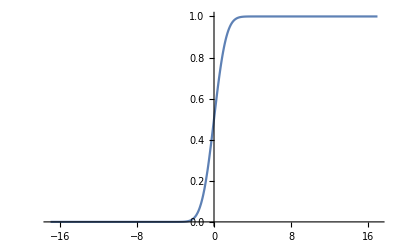

```mathematica
Plot[1/2 Erfc[-x/(√2)],{x,-16.970562748477143,16.970562748477143}]
```

```mathematica
1/2 Erfc[-x/(√2)]
```

1/2 Erfc[-x/(√2)]

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
(1-1/2 Erfc[-x/(√2)])x+ ((1/2 Erfc[-x/(√2)])((ⅇ^(-x^2/2))/(√(2 π))))
```

x (1-1/2 Erfc[-x/(√2)])+(ⅇ^(-x^2/2) Erfc[-x/(√2)])/(2 √(2 π))

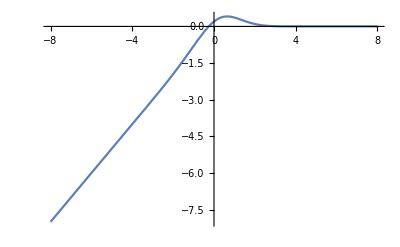

```mathematica
Plot[x (1-1/2 Erfc[-x/(√2)])+(ⅇ^(-x^2/2) Erfc[-x/(√2)])/(2 √(2 π)),{x,-8,8}]
```

```mathematica
FullSimplify[
Normalize@{x,x (1-1/2 Erfc[-x/(√2)])+(ⅇ^(-x^2/2) Erfc[-x/(√2)])/(2 √(2 π))}.
Normalize@{x,x},
x∈Reals]
```

(x (1+Erf[x/(√2)]+ⅇ^(x^2/2) √(2 π) x (2+Erfc[x/(√2)])))/(√2 √(x^2 ((1+Erf[x/(√2)])^2-2 ⅇ^(x^2/2) √(2 π) x (-1+Erf[x/(√2)]^2)+2 ⅇ^(x^2) π x^2 (4+Erfc[x/(√2)]^2))))

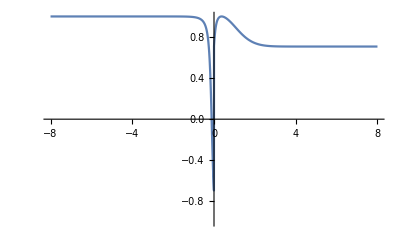

```mathematica
Plot[(x (1+Erf[x/(√2)]+ⅇ^(x^2/2) √(2 π) x (2+Erfc[x/(√2)])))/(√2 √(x^2 ((1+Erf[x/(√2)])^2-2 ⅇ^(x^2/2) √(2 π) x (-1+Erf[x/(√2)]^2)+2 ⅇ^(x^2) π x^2 (4+Erfc[x/(√2)]^2)))),{x,-8,8},PlotRange->{-1,1}]
```

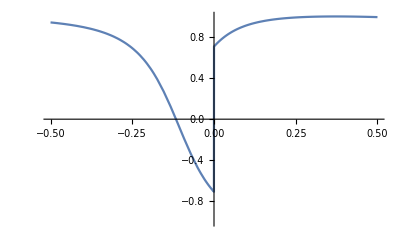

```mathematica
Plot[(x (1+Erf[x/(√2)]+ⅇ^(x^2/2) √(2 π) x (2+Erfc[x/(√2)])))/(√2 √(x^2 ((1+Erf[x/(√2)])^2-2 ⅇ^(x^2/2) √(2 π) x (-1+Erf[x/(√2)]^2)+2 ⅇ^(x^2) π x^2 (4+Erfc[x/(√2)]^2)))),{x,-1/2,1/2},PlotRange->{-1,1}]
```

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
With[{f=Identity,g=Function[x,x^3],a=ⅇ^(-x^2/2)},
(1-a)f[x]+a g[x]
]
```

(1-ⅇ^(-x^2/2)) x+ⅇ^(-x^2/2) x^3

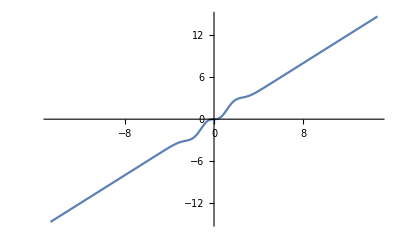

```mathematica
Plot[(1-ⅇ^(-x^2/2)) x+ⅇ^(-x^2/2) x^3,{x,-14.696938456699069,14.696938456699069}]
```

```mathematica
(1-ⅇ^(-x^2/2)) x+ⅇ^(-x^2/2) x^3
```

```mathematica
With[{f=Identity,g=Function[x,x^3-x],a=ⅇ^(-x^2/2)},
(1-a)f[x]+a g[x]
]
```

(1-ⅇ^(-x^2/2)) x+ⅇ^(-x^2/2) (-x+x^3)

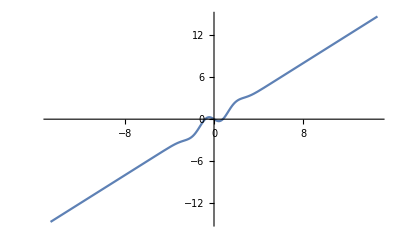

```mathematica
Plot[(1-ⅇ^(-x^2/2)) x+ⅇ^(-x^2/2) (-x+x^3),{x,-14.696938456699069,14.696938456699069}]
```

```mathematica
With[{f=Identity,g=Function[x,x^2-x],a=ⅇ^(-x^2/2)},
(1-a)g[x]+a f[x]
]
```

ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) (-x+x^2)

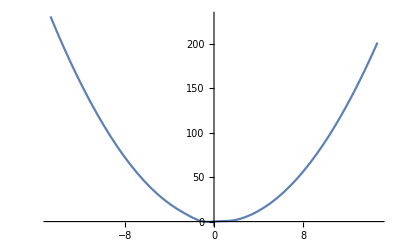

```mathematica
Plot[ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) (-x+x^2),{x,-14.696938456699069,14.696938456699069}]
```

```mathematica
With[{f=Identity,g=Function[x,x^3-x],a=ⅇ^(-x^2/2)},
(1-a)g[x]+a f[x]
]
```

ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) (-x+x^3)

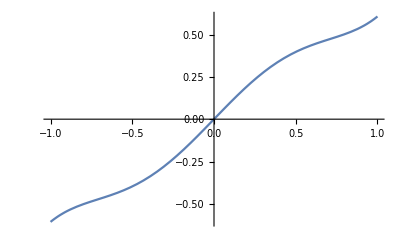

```mathematica
Plot[ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) (-x+x^3),{x,-1,1}]
```

```mathematica
With[{f=Function[x,x^2],g=Function[x,x^3-x],a=ⅇ^(-x^2/2)},
(1-a)g[x]+a f[x]
]
```

ⅇ^(-x^2/2) x^2+(1-ⅇ^(-x^2/2)) (-x+x^3)

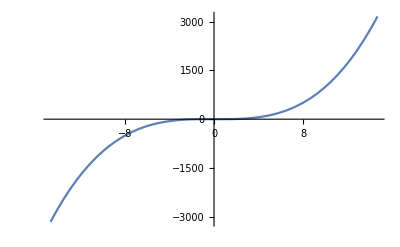

```mathematica
Plot[ⅇ^(-x^2/2) x^2+(1-ⅇ^(-x^2/2)) (-x+x^3),{x,-14.696938456699069,14.696938456699069}]
```

```mathematica
With[{f=Function[x,x^2],g=Exp,a=ⅇ^(-x^2/2)},
(1-a)g[x]+a f[x]
]
```

```mathematica
Sinc[x]
```

Sinc[x]

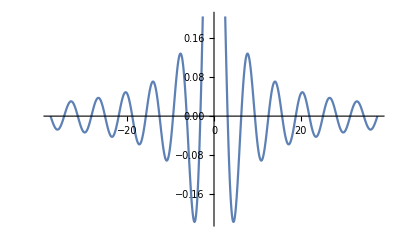

```mathematica
Plot[Sinc[x],{x,-37.69911184307752,37.69911184307752}]
```

```mathematica
With[{f=Sinc,g=Exp,a=ⅇ^(-x^2/2)},
(1-a)g[x]+a f[x]
]
```

ⅇ^x (1-ⅇ^(-x^2/2))+ⅇ^(-x^2/2) Sinc[x]

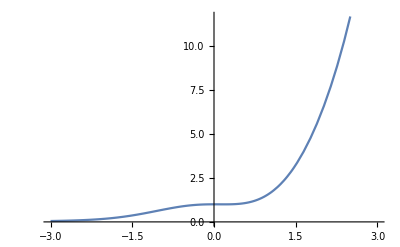

```mathematica
Plot[ⅇ^x (1-ⅇ^(-x^2/2))+ⅇ^(-x^2/2) Sinc[x],{x,-3,3}]
```

```mathematica
(1-a[x])f[x]+a[x] g[x]
```

(1-a[x]) f[x]+a[x] g[x]

```mathematica
With[{f=Exp,g=Sinc,a=ⅇ^(-x^2/2)},
(1-a)g[x]+a f[x]
]
```

ⅇ^(x-x^2/2)+(1-ⅇ^(-x^2/2)) Sinc[x]

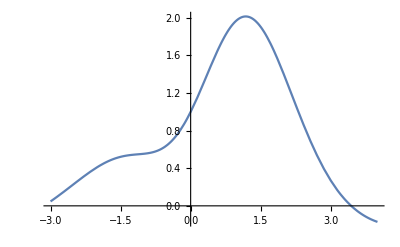

```mathematica
Plot[ⅇ^(x-x^2/2)+(1-ⅇ^(-x^2/2)) Sinc[x],{x,-3,4}]
```

```mathematica
With[{f=Function[x,-x],g=Identity,a=ⅇ^(-x^2/2)},
(1-a)g[x]+a f[x]
]
```

-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) x

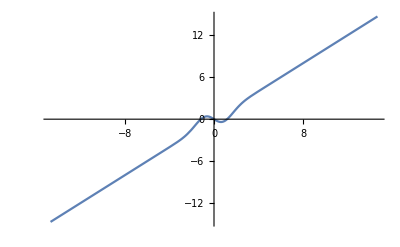

```mathematica
Plot[-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) x,{x,-14.696938456699069,14.696938456699069}]
```

```mathematica
FullSimplify[
Normalize@{x,-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) x}.
Normalize@{x,x},
x∈Reals]
```

(-1+ⅇ^(x^2/2))/(√(2-2 ⅇ^(x^2/2)+ⅇ^(x^2)))

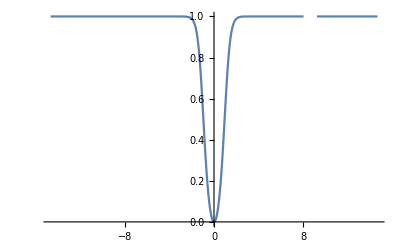

```mathematica
Plot[(-1+ⅇ^(x^2/2))/(√(2-2 ⅇ^(x^2/2)+ⅇ^(x^2))),{x,-14.696938456699069,14.696938456699069},PlotRange->{0,1}]
```

```mathematica
FullSimplify[
Normalize@{x,-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) x}.
Normalize@{x,-x},
x∈Reals]
```

1/(√(2-2 ⅇ^(x^2/2)+ⅇ^(x^2)))

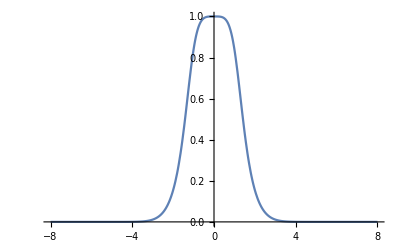

```mathematica
Plot[1/(√(2-2 ⅇ^(x^2/2)+ⅇ^(x^2))),{x,-8,8}]
```

```mathematica
FullSimplify[
Normalize@{x,(1-a)g[x]+a f[x]}.
Normalize@{x,f[x]},
{a,x,f[x],g[x]}∈Reals]
```

(x^2+f[x] (a f[x]+g[x]-a g[x]))/(√((x^2+f[x]^2) (x^2+(a f[x]+g[x]-a g[x])^2)))

```mathematica
(x^2+f[x] (a f[x]+g[x]-a g[x]))/(√((x^2+f[x]^2) (x^2+(a f[x]+g[x]-a g[x])^2)))==a
```

(x^2+f[x] (a f[x]+g[x]-a g[x]))/(√((x^2+f[x]^2) (x^2+(a f[x]+g[x]-a g[x])^2)))==a

```mathematica
Reduce[(x^2+f[x] (a f[x]+g[x]-a g[x]))/(√((x^2+f[x]^2) (x^2+(a f[x]+g[x]-a g[x])^2)))==a]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[(x^2+f[x] (a f[x]+g[x]-a g[x]))/(√((x^2+f[x]^2) (x^2+(a f[x]+g[x]-a g[x])^2)))==a]

```mathematica
ExpandAll@((x^2+f[x] (a f[x]+g[x]-a g[x]))/(√((x^2+f[x]^2) (x^2+(a f[x]+g[x]-a g[x])^2))))
```

x^2/(√(x^4+x^2 f[x]^2+a^2 x^2 f[x]^2+a^2 f[x]^4+2 a x^2 f[x] g[x]-2 a^2 x^2 f[x] g[x]+2 a f[x]^3 g[x]-2 a^2 f[x]^3 g[x]+x^2 g[x]^2-2 a x^2 g[x]^2+a^2 x^2 g[x]^2+f[x]^2 g[x]^2-2 a f[x]^2 g[x]^2+a^2 f[x]^2 g[x]^2))+(a f[x]^2)/(√(x^4+x^2 f[x]^2+a^2 x^2 f[x]^2+a^2 f[x]^4+2 a x^2 f[x] g[x]-2 a^2 x^2 f[x] g[x]+2 a f[x]^3 g[x]-2 a^2 f[x]^3 g[x]+x^2 g[x]^2-2 a x^2 g[x]^2+a^2 x^2 g[x]^2+f[x]^2 g[x]^2-2 a f[x]^2 g[x]^2+a^2 f[x]^2 g[x]^2))+(f[x] g[x])/(√(x^4+x^2 f[x]^2+a^2 x^2 f[x]^2+a^2 f[x]^4+2 a x^2 f[x] g[x]-2 a^2 x^2 f[x] g[x]+2 a f[x]^3 g[x]-2 a^2 f[x]^3 g[x]+x^2 g[x]^2-2 a x^2 g[x]^2+a^2 x^2 g[x]^2+f[x]^2 g[x]^2-2 a f[x]^2 g[x]^2+a^2 f[x]^2 g[x]^2))-(a f[x] g[x])/(√(x^4+x^2 f[x]^2+a^2 x^2 f[x]^2+a^2 f[x]^4+2 a x^2 f[x] g[x]-2 a^2 x^2 f[x] g[x]+2 a f[x]^3 g[x]-2 a^2 f[x]^3 g[x]+x^2 g[x]^2-2 a x^2 g[x]^2+a^2 x^2 g[x]^2+f[x]^2 g[x]^2-2 a f[x]^2 g[x]^2+a^2 f[x]^2 g[x]^2))

```mathematica
Composition[Identity][(x^2+f[x] (a f[x]+g[x]-a g[x]))/(√((x^2+f[x]^2) (x^2+(a f[x]+g[x]-a g[x])^2)))]
```

(x^2+f[x] (a f[x]+g[x]-a g[x]))/(√((x^2+f[x]^2) (x^2+(a f[x]+g[x]-a g[x])^2)))

```mathematica
Composition[Function[x,x^2]][(x^2+f[x] (a f[x]+g[x]-a g[x]))/(√((x^2+f[x]^2) (x^2+(a f[x]+g[x]-a g[x])^2)))]
```

((x^2+f[x] (a f[x]+g[x]-a g[x]))^2)/((x^2+f[x]^2) (x^2+(a f[x]+g[x]-a g[x])^2))

```mathematica
Composition[Function[x,x^2]][(x^2+f[x] (a f[x]+g[x]-a g[x]))/(√((x^2+f[x]^2) (x^2+(a f[x]+g[x]-a g[x])^2)))]
```

```mathematica
ExpandAll@(((x^2+f[x] (a f[x]+g[x]-a g[x]))^2)/((x^2+f[x]^2) (x^2+(a f[x]+g[x]-a g[x])^2)))
```

x^4/(x^4+x^2 f[x]^2+a^2 x^2 f[x]^2+a^2 f[x]^4+2 a x^2 f[x] g[x]-2 a^2 x^2 f[x] g[x]+2 a f[x]^3 g[x]-2 a^2 f[x]^3 g[x]+x^2 g[x]^2-2 a x^2 g[x]^2+a^2 x^2 g[x]^2+f[x]^2 g[x]^2-2 a f[x]^2 g[x]^2+a^2 f[x]^2 g[x]^2)+(2 a x^2 f[x]^2)/(x^4+x^2 f[x]^2+a^2 x^2 f[x]^2+a^2 f[x]^4+2 a x^2 f[x] g[x]-2 a^2 x^2 f[x] g[x]+2 a f[x]^3 g[x]-2 a^2 f[x]^3 g[x]+x^2 g[x]^2-2 a x^2 g[x]^2+a^2 x^2 g[x]^2+f[x]^2 g[x]^2-2 a f[x]^2 g[x]^2+a^2 f[x]^2 g[x]^2)+(a^2 f[x]^4)/(x^4+x^2 f[x]^2+a^2 x^2 f[x]^2+a^2 f[x]^4+2 a x^2 f[x] g[x]-2 a^2 x^2 f[x] g[x]+2 a f[x]^3 g[x]-2 a^2 f[x]^3 g[x]+x^2 g[x]^2-2 a x^2 g[x]^2+a^2 x^2 g[x]^2+f[x]^2 g[x]^2-2 a f[x]^2 g[x]^2+a^2 f[x]^2 g[x]^2)+(2 x^2 f[x] g[x])/(x^4+x^2 f[x]^2+a^2 x^2 f[x]^2+a^2 f[x]^4+2 a x^2 f[x] g[x]-2 a^2 x^2 f[x] g[x]+2 a f[x]^3 g[x]-2 a^2 f[x]^3 g[x]+x^2 g[x]^2-2 a x^2 g[x]^2+a^2 x^2 g[x]^2+f[x]^2 g[x]^2-2 a f[x]^2 g[x]^2+a^2 f[x]^2 g[x]^2)-(2 a x^2 f[x] g[x])/(x^4+x^2 f[x]^2+a^2 x^2 f[x]^2+a^2 f[x]^4+2 a x^2 f[x] g[x]-2 a^2 x^2 f[x] g[x]+2 a f[x]^3 g[x]-2 a^2 f[x]^3 g[x]+x^2 g[x]^2-2 a x^2 g[x]^2+a^2 x^2 g[x]^2+f[x]^2 g[x]^2-2 a f[x]^2 g[x]^2+a^2 f[x]^2 g[x]^2)+(2 a f[x]^3 g[x])/(x^4+x^2 f[x]^2+a^2 x^2 f[x]^2+a^2 f[x]^4+2 a x^2 f[x] g[x]-2 a^2 x^2 f[x] g[x]+2 a f[x]^3 g[x]-2 a^2 f[x]^3 g[x]+x^2 g[x]^2-2 a x^2 g[x]^2+a^2 x^2 g[x]^2+f[x]^2 g[x]^2-2 a f[x]^2 g[x]^2+a^2 f[x]^2 g[x]^2)-(2 a^2 f[x]^3 g[x])/(x^4+x^2 f[x]^2+a^2 x^2 f[x]^2+a^2 f[x]^4+2 a x^2 f[x] g[x]-2 a^2 x^2 f[x] g[x]+2 a f[x]^3 g[x]-2 a^2 f[x]^3 g[x]+x^2 g[x]^2-2 a x^2 g[x]^2+a^2 x^2 g[x]^2+f[x]^2 g[x]^2-2 a f[x]^2 g[x]^2+a^2 f[x]^2 g[x]^2)+(f[x]^2 g[x]^2)/(x^4+x^2 f[x]^2+a^2 x^2 f[x]^2+a^2 f[x]^4+2 a x^2 f[x] g[x]-2 a^2 x^2 f[x] g[x]+2 a f[x]^3 g[x]-2 a^2 f[x]^3 g[x]+x^2 g[x]^2-2 a x^2 g[x]^2+a^2 x^2 g[x]^2+f[x]^2 g[x]^2-2 a f[x]^2 g[x]^2+a^2 f[x]^2 g[x]^2)-(2 a f[x]^2 g[x]^2)/(x^4+x^2 f[x]^2+a^2 x^2 f[x]^2+a^2 f[x]^4+2 a x^2 f[x] g[x]-2 a^2 x^2 f[x] g[x]+2 a f[x]^3 g[x]-2 a^2 f[x]^3 g[x]+x^2 g[x]^2-2 a x^2 g[x]^2+a^2 x^2 g[x]^2+f[x]^2 g[x]^2-2 a f[x]^2 g[x]^2+a^2 f[x]^2 g[x]^2)+(a^2 f[x]^2 g[x]^2)/(x^4+x^2 f[x]^2+a^2 x^2 f[x]^2+a^2 f[x]^4+2 a x^2 f[x] g[x]-2 a^2 x^2 f[x] g[x]+2 a f[x]^3 g[x]-2 a^2 f[x]^3 g[x]+x^2 g[x]^2-2 a x^2 g[x]^2+a^2 x^2 g[x]^2+f[x]^2 g[x]^2-2 a f[x]^2 g[x]^2+a^2 f[x]^2 g[x]^2)

```mathematica
FullSimplify[%90]
```

((x^2+f[x] (a f[x]+g[x]-a g[x]))^2)/((x^2+f[x]^2) (x^2+(a f[x]+g[x]-a g[x])^2))

```mathematica
Cancel[((x^2+f[x] (a f[x]+g[x]-a g[x]))^2)/((x^2+f[x]^2) (x^2+(a f[x]+g[x]-a g[x])^2))]
```

(x^2+a f[x]^2+f[x] g[x]-a f[x] g[x])^2/((x^2+f[x]^2) (x^2+a^2 f[x]^2+2 a f[x] g[x]-2 a^2 f[x] g[x]+g[x]^2-2 a g[x]^2+a^2 g[x]^2))

```mathematica
TraditionalForm@((x^2+f[x] (a f[x]+g[x]-a g[x]))/(√((x^2+f[x]^2) (x^2+(a f[x]+g[x]-a g[x])^2))))==a
```

(f(x) (a f(x)-a g(x)+g(x))+x^2)/(√(((f(x))^2+x^2) ((a f(x)-a g(x)+g(x))^2+x^2)))==a

```mathematica
Reduce[(x^2+f[x] (a f[x]+g[x]-a g[x]))/(√((x^2+f[x]^2) (x^2+(a f[x]+g[x]-a g[x])^2)))==a
```

```mathematica
With[{f=Function[x,-x],g=Identity,a=ⅇ^(-x^2/2)},
(1-a)g'[x]+a f'[x]
]
```

1-2 ⅇ^(-x^2/2)

```mathematica
∫(1-2 ⅇ^(-x^2/2))ⅆx
```

x-√(2 π) Erf[x/(√2)]

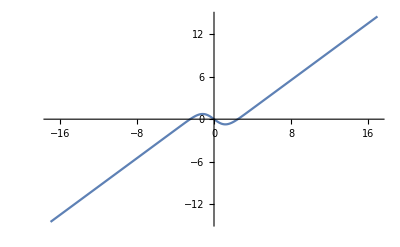

```mathematica
Plot[x-√(2 π) Erf[x/(√2)],{x,-16.970562748477143,16.970562748477143}]
```

```mathematica
x-√(2 π) Erf[x/(√2)]==-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) x
```

x-√(2 π) Erf[x/(√2)]==-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) x

```mathematica
Reduce[x-√(2 π) Erf[x/(√2)]==-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) x]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[x-√(2 π) Erf[x/(√2)]==-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) x]

```mathematica
f[x+α]==f[x]+f'[x]∫_a^(x+α) √(1+f'[x])ⅆx
```

f[x+α]==f[x]+(∫_a^(x+α) √(1+f'[x])ⅆx) f'[x]

```mathematica
With[{f=Identity},
f[x+α]==f[x]+f'[x]∫_a^(x+α) √(1+f'[x])ⅆx
]
```

x+α==x+√2 (-a+x+α)

```mathematica
With[{f=Identity,α=1},
f[x+α]==f[x]+f'[x]∫_x^(x+α) √(1+f'[x])ⅆx
]
```

1+x==√2+x

```mathematica
With[{f=Identity,α=1},
f[x+α]==f[x]+∫_x^(x+α) f'[x]ⅆx
]
```

True

```mathematica
With[{f=Identity,α=1},
f[x+α]==f[x]+∫_x^(x+α) f'[x]ⅆx
]
```

```mathematica
With[{f=Identity,α=1},
f[x+α]==f[x]+∫_x^(x+α) f'[x] √(1+f'[x])ⅆx
]
```

1+x==√2+x

```mathematica
With[{f=Identity,α=1},
f[x+α]==f[x]+∫_x^(x+α) f[x] √(1+f'[x])ⅆx
]
```

1+x==x+√2 (-x^2/2+1/2 (1+x)^2)

```mathematica
With[{f=Identity,α=1},
f[x+α]==f[x]+f[x]∫_x^(x+α) √(1+f'[x])ⅆx
]
```

1+x==x+√2 x

```mathematica
With[{f=Identity,α=1},
f[x+α]==f[x]+f[x]∫_x^(x+α) √(1+f'[x])ⅆx
]
```

```mathematica
With[{f=Identity,α=1},
f[x+α]==f[x]+∫_x^(x+α) √(1+f'[x])ⅆx
]
```

1+x==√2+x

```mathematica
With[{f=Identity,α=1},
f[x+α]==f[x]+∫_x^(x+α) f'[x]ⅆx
]
```

True

```mathematica
FullSimplify[1==∫_0^a x^2 ⅆx,x∈Reals∧a∈]
```

a^3==3

```mathematica
PositiveReals
```

```mathematica
Solve[FullSimplify[1==∫_0^a x^2 ⅆx,x∈Reals∧a∈],a]
```

{{a→-(-3)^(1/3)},{a→3^(1/3)},{a→(-1)^(2/3) 3^(1/3)}}

```mathematica
FullSimplify[
Reduce[
FullSimplify[
1==∫_0^a x^2 ⅆx,x∈Reals∧a∈],
a],
a∈PositiveReals]
```

a==3^(1/3)

```mathematica
3^(1/3)
```

```mathematica
FullSimplify[
Reduce[
FullSimplify[
1==∫_0^a √(1+4 x^2)ⅆx,x∈Reals∧a∈],
a],
a∈PositiveReals]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

False

```mathematica
Reduce[
FullSimplify[
1==∫_0^a √(1+4 x^2)ⅆx,x∈Reals∧a∈],
a]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[2 a √(1+4 a^2)+ArcSinh[2 a]==4,a]

```mathematica
FullSimplify[
1==∫_0^a √(1+4 x^2)ⅆx,x∈Reals∧a∈]
```

2 a √(1+4 a^2)+ArcSinh[2 a]==4

```mathematica
ContourPlot[2 a √(1+4 a^2)+ArcSinh[2 a]==4,{a,-2,2}]
```

ContourPlot::argrx: ContourPlot called with 2 arguments; 3 arguments are expected.

ContourPlot[2 a √(1+4 a^2)+ArcSinh[2 a]==4,{a,-2,2}]

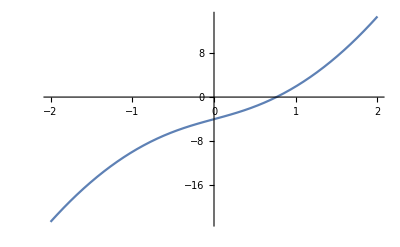

```mathematica
Plot[2 a √(1+4 a^2)+ArcSinh[2 a]==4,{a,-2,2}]
```

```mathematica
Solve[2 a √(1+4 a^2)+ArcSinh[2 a]==4,a,Reals]
```

{{a→Root0.764Root[{-4+Log[2 #1+√(1+4 #1^2)]+2 #1 √(1+4 #1^2)&,0.76392666331709104116}]0.763926663317091}}

```mathematica
N[{{a->Root[{-4+Log[2 #1+√(1+4 #1^2)]+2 #1 √(1+4 #1^2)&,0.76392666331709104116192058753047333663`20.30193885116719}]}}]
```

{{a→0.763927}}

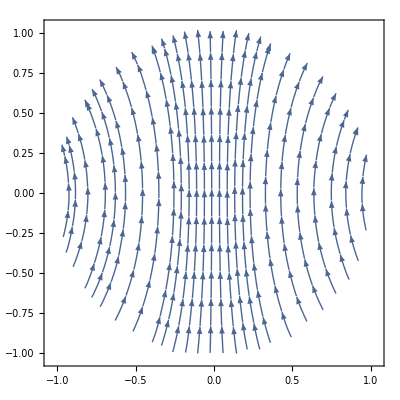

```mathematica
StreamPlot[
{Sin[x y],Cos[x y^2]},
{x,y}∈Disk[]]
```

```mathematica
With[{f={x,x^3+x^2+x}},
Grid@
Map[
Function[p,
{p,FullSimplify[Normalize@p.Normalize@f,Element[x,Reals]]}
],{{x,x^3},{x,x^2},{x,x}}]
]
```

{x,x^3} | ((1+x^2+x^3+x^4) Abs[x])/(√((1+x^4) (x^2+(x+x^2+x^3)^2)))
{x,x^2} | (1+x)/(√(2+x (2+x)))
{x,x} | (2+x+x^2)/(√2 √((1+x^2) (2+x (2+x))))

```mathematica
With[{f={x,x^3+x^2+x}},
Map[
Function[p,
FullSimplify[Normalize@p.Normalize@f,Element[x,Reals]]
],{{x,x^3},{x,x^2},{x,x}}]
]
```

{((1+x^2+x^3+x^4) Abs[x])/(√((1+x^4) (x^2+(x+x^2+x^3)^2))),(1+x)/(√(2+x (2+x))),(2+x+x^2)/(√2 √((1+x^2) (2+x (2+x))))}

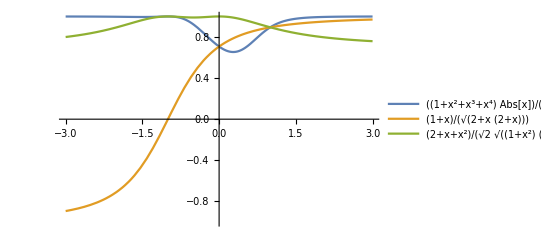

```mathematica
Plot[
{((1+x^2+x^3+x^4) Abs[x])/(√((1+x^4) (x^2+(x+x^2+x^3)^2))),(1+x)/(√(2+x (2+x))),(2+x+x^2)/(√2 √((1+x^2) (2+x (2+x))))},
{x,-3,3},PlotLegends->"Expressions",PlotRange->{-1,1}]
```

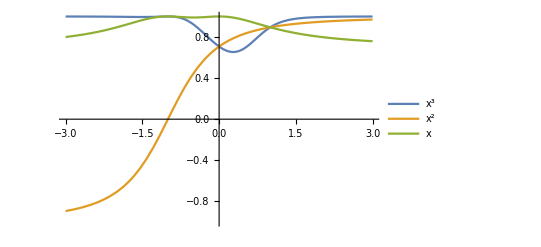

```mathematica
Plot[
{((1+x^2+x^3+x^4) Abs[x])/(√((1+x^4) (x^2+(x+x^2+x^3)^2))),(1+x)/(√(2+x (2+x))),(2+x+x^2)/(√2 √((1+x^2) (2+x (2+x))))},
{x,-3,3},PlotLegends->{x^3,x^2,x},PlotRange->{-1,1}]
```

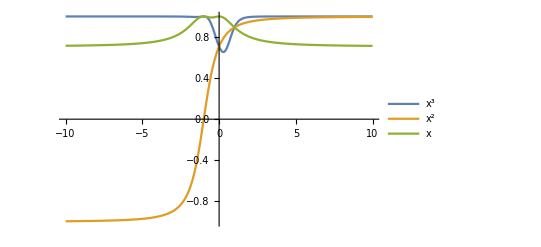

```mathematica
Plot[
{((1+x^2+x^3+x^4) Abs[x])/(√((1+x^4) (x^2+(x+x^2+x^3)^2))),(1+x)/(√(2+x (2+x))),(2+x+x^2)/(√2 √((1+x^2) (2+x (2+x))))},
{x,-10,10},PlotLegends->{x^3,x^2,x},PlotRange->{-1,1}]
```

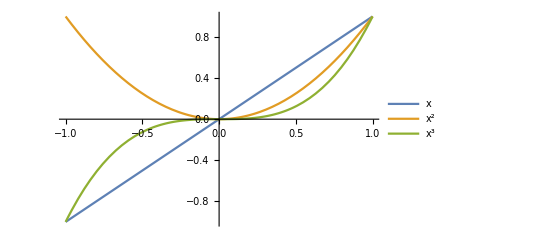

```mathematica
Plot[
{x,x^2,x^3},
{x,-1,1},PlotLegends->"Expressions"]
```

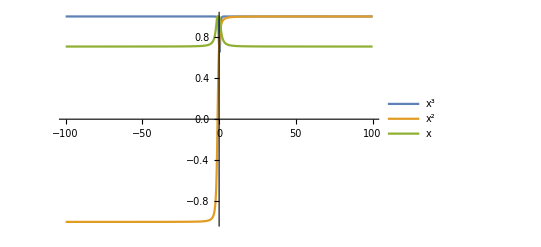

```mathematica
Plot[
{((1+x^2+x^3+x^4) Abs[x])/(√((1+x^4) (x^2+(x+x^2+x^3)^2))),(1+x)/(√(2+x (2+x))),(2+x+x^2)/(√2 √((1+x^2) (2+x (2+x))))},
{x,-100,100},PlotLegends->{x^3,x^2,x},PlotRange->{-1,1}]
```

```mathematica
f:Reals->Integers
```

f:ℝ→ℤ

```mathematica
ζ[x]
```

ζ[x]

```mathematica
Manipulate[
With[{poly=Table[x^i,{i,0,a,1}]},
With[{f=Total@poly},
With[{dots=Map[
Function[p,
FullSimplify[Normalize@{x,p}.Normalize@f,Element[x,Reals]]
],poly]},
Plot[
dots,
{x,-10,10},PlotLegends->poly,PlotRange->{-1,1}]
]]],{a,0,10,1}]
```

```mathematica
Manipulate[
With[{poly=Table[x^i,{i,0,a,1}]},
With[{f=Total@poly},
With[{dots=Map[
Function[p,
FullSimplify[Normalize@{x,p}.Normalize@f,Element[x,Reals]]
],poly]},
dots
]]],{a,0,10,1}]
```

```mathematica
Manipulate[
With[{poly=Table[x^i,{i,0,a,1}]},
With[{f=Total@poly},
With[{dots=Map[
Function[p,
FullSimplify[Normalize@{x,p}.
Normalize@{x,f},Element[x,Reals]]
],poly]},
Plot[
dots,
{x,-10,10},PlotLegends->poly,PlotRange->{-1,1}]
]]],{a,0,10,1}]
```

```mathematica
FullSimplify[
Normalize[{x,Exp[x]}].
Normalize[{x,Log[x]}]
,x∈Reals]
```

(x^2+ⅇ^x Log[x])/(√((ⅇ^(2 x)+x^2) (x^2+Abs[Log[x]]^2)))

```mathematica
FullSimplify[
Normalize[{x,Exp[x]}].
Normalize[{x,Log[x]}]
,{x,Log[x]}∈Reals]
```

(x^2+ⅇ^x Log[x])/(√((ⅇ^(2 x)+x^2) (x^2+Log[x]^2)))

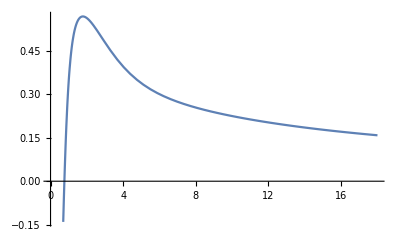

```mathematica
Plot[(x^2+ⅇ^x Log[x])/(√((ⅇ^(2 x)+x^2) (x^2+Log[x]^2))),{x,0,18.}]
```

```mathematica
With[{f=Identity,g=Identity},
FullSimplify[
Normalize[{x,f[x]}].
Normalize[{x,g[x]}]
,{x,Log[x]}∈Reals]
]
```

1

```mathematica
With[{f=Identity,g=Identity},
FullSimplify[
Normalize[{x,f[x]}].
Normalize[{x,g[x]}]
,{x,f[x],g[x]}∈Reals]
]
```

1

```mathematica
With[{f=Identity,g=Sin},
FullSimplify[
Normalize[{x,f[x]}].
Normalize[{x,g[x]}]
,{x,f[x],g[x]}∈Reals]
]
```

(Sign[x] (x+Sin[x]))/(√(1+2 x^2-Cos[2 x]))

```mathematica
With[{f=Cos,g=Sin},
FullSimplify[
Normalize[{x,f[x]}].
Normalize[{x,g[x]}]
,{x,f[x],g[x]}∈Reals]
]
```

(x^2+Cos[x] Sin[x])/(√((x^2+Cos[x]^2) (x^2+Sin[x]^2)))

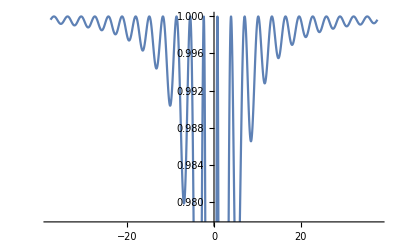

```mathematica
Plot[(x^2+Cos[x] Sin[x])/(√((x^2+Cos[x]^2) (x^2+Sin[x]^2))),{x,-37.69911184307752,37.69911184307752}]
```

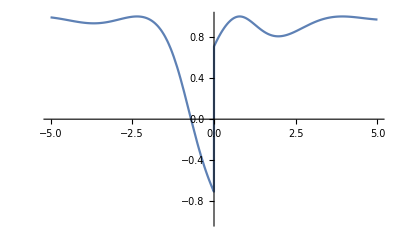

```mathematica
Plot[(x^2+Cos[x] Sin[x])/(√((x^2+Cos[x]^2) (x^2+Sin[x]^2))),{x,-5,5},PlotRange->{-1,1}]
```

```mathematica
With[{f=Function[x,x^2],g=Function[x,√x]},
FullSimplify[
Normalize[{x,f[x]}].
Normalize[{x,g[x]}]
,{x,f[x],g[x]}∈Reals]
]
```

(x^2+x^(5/2))/(Abs[x]^(3/2) √((1+x^2) (1+Abs[x])))

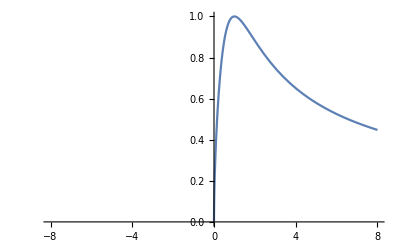

```mathematica
Plot[(x^2+x^(5/2))/(Abs[x]^(3/2) √((1+x^2) (1+Abs[x]))),{x,-8,8}]
```

```mathematica
With[{f=Function[x,Exp[x]],g=Function[x,Log[x]]},
FullSimplify[
Normalize[{x,f[x]}].
Normalize[{x,g[x]}]
,{x,f[x],g[x]}∈Reals]
]
```

(x^2+ⅇ^x Log[x])/(√((ⅇ^(2 x)+x^2) (x^2+Log[x]^2)))

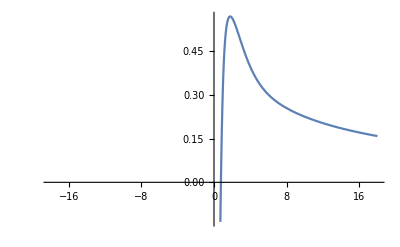

```mathematica
Plot[(x^2+ⅇ^x Log[x])/(√((ⅇ^(2 x)+x^2) (x^2+Log[x]^2))),{x,-18.,18.}]
```

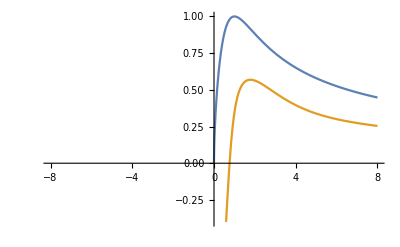

```mathematica
Plot[
{(x^2+x^(5/2))/(Abs[x]^(3/2) √((1+x^2) (1+Abs[x]))),(x^2+ⅇ^x Log[x])/(√((ⅇ^(2 x)+x^2) (x^2+Log[x]^2)))}
,{x,-8,8}]
```

```mathematica
With[{f=Function[x,2^x],g=Function[x,Log[2,x]]},
FullSimplify[
Normalize[{x,f[x]}].
Normalize[{x,g[x]}]
,{x,f[x],g[x]}∈Reals]
]
```

(x^2 Log[2]+2^x Log[x])/(√((4^x+x^2) (x^2 Log[2]^2+Log[x]^2)))

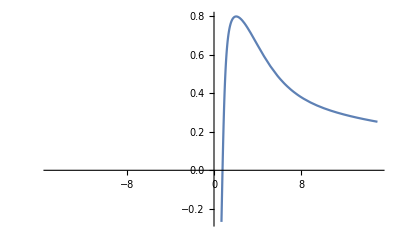

```mathematica
Plot[(x^2 Log[2]+2^x Log[x])/(√((4^x+x^2) (x^2 Log[2]^2+Log[x]^2))),{x,-15.,15.}]
```

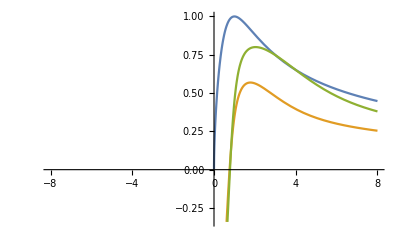

```mathematica
Plot[
{(x^2+x^(5/2))/(Abs[x]^(3/2) √((1+x^2) (1+Abs[x]))),(x^2+ⅇ^x Log[x])/(√((ⅇ^(2 x)+x^2) (x^2+Log[x]^2))),(x^2 Log[2]+2^x Log[x])/(√((4^x+x^2) (x^2 Log[2]^2+Log[x]^2)))}
,{x,-8,8}]
```

```mathematica
With[{f=Function[x,-1/3-(2 2^(1/3))/(3 (-20+27 x+3 √3 √(16-40 x+27 x^2))^(1/3))+((-20+27 x+3 √3 √(16-40 x+27 x^2))^(1/3))/(3 2^(1/3))],g=Function[x,x^3+x^2+x+1]},
FullSimplify[
Normalize[{x,f[x]}].
Normalize[{x,g[x]}]
,{x,f[x],g[x]}∈Reals]
]
```

(x^2+1/6 (1+x) (1+x^2) (-2-(4 2^(1/3))/(-20+27 x+3 √(48+3 x (-40+27 x)))^(1/3)+2^(2/3) (-20+27 x+3 √(48+3 x (-40+27 x)))^(1/3)))/(√((x^2+(1+x+x^2+x^3)^2) (x^2+1/36 (2+(4 2^(1/3))/(-20+27 x+3 √(48+3 x (-40+27 x)))^(1/3)-2^(2/3) (-20+27 x+3 √(48+3 x (-40+27 x)))^(1/3))^2)))

```mathematica
InverseFunction[Function[x,x^3+x^2+x+1]]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Function[x,-1/3-(2 2^(1/3))/(3 (-20+27 x+3 √3 √(16-40 x+27 x^2))^(1/3))+((-20+27 x+3 √3 √(16-40 x+27 x^2))^(1/3))/(3 2^(1/3))]

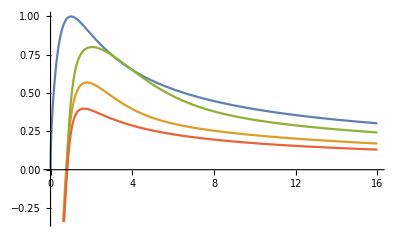

```mathematica
Plot[{
(x^2+x^(5/2))/(Abs[x]^(3/2) √((1+x^2) (1+Abs[x]))),
(x^2+ⅇ^x Log[x])/(√((ⅇ^(2 x)+x^2) (x^2+Log[x]^2))),
(x^2 Log[2]+2^x Log[x])/(√((4^x+x^2) (x^2 Log[2]^2+Log[x]^2))),
(x^2+1/6 (1+x) (1+x^2) (-2-(4 2^(1/3))/(-20+27 x+3 √(48+3 x (-40+27 x)))^(1/3)+2^(2/3) (-20+27 x+3 √(48+3 x (-40+27 x)))^(1/3)))/(√((x^2+(1+x+x^2+x^3)^2) (x^2+1/36 (2+(4 2^(1/3))/(-20+27 x+3 √(48+3 x (-40+27 x)))^(1/3)-2^(2/3) (-20+27 x+3 √(48+3 x (-40+27 x)))^(1/3))^2)))
},{x,0,16}]
```

```mathematica
Exp[π ⅈ]
```

-1

```mathematica
Log[-1]
```

ⅈ π

```mathematica
ReImPlot[Exp[z],{z,-2-2I,2+2I}]
```

ReImPlot::plln: Limiting value -2-2 ⅈ in {z,-2-2 ⅈ,2+2 ⅈ} is not a machine-sized real number.

ReImPlot[Exp[z],{z,-2-2 ⅈ,2+2 ⅈ}]

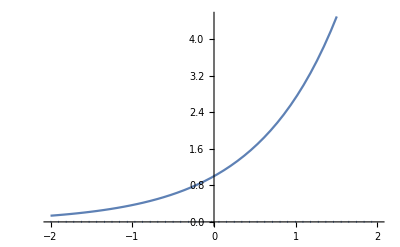

```mathematica
ReImPlot[Exp[z],{z,-2,2}]
```

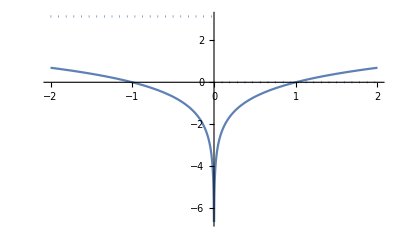

```mathematica
ReImPlot[Log[z],{z,-2,2}]
```

```mathematica
Log[0]
```

-∞

```mathematica
Log[-1]
```

ⅈ π